# std::Math An implementation of standard math functions in Rust, rather than importing from a C library.

## pow(mantissa: float, exponent: float)

```mathematica
TaylorSeries[Log[x],{x,0,10}]
```

TaylorSeries[Log[x],{x,0,10}]

## sin(angle: float)

theta-theta^3/6+theta^5/120-theta^7/5040+theta^9/362880-theta^11/39916800+theta^13/6227020800-theta^15/1307674368000

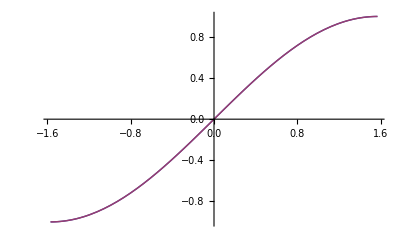

5.40412×10^-12

```mathematica
clear[f,theta,g];
sinApprox[theta_] = Normal[Series[Sin[theta],{theta,0,15}]]
Plot[{Sin[theta],sinApprox[theta]},{theta, -Pi/2,Pi/2}]
Evaluate[Abs[Sin[Pi/2-.01]-sinApprox[Pi/2-.01]]]
```

This Taylor Series is accurate in computing the sin of π/2 up to the 38th bit. This approximation is appropriate for 32-bit floating point integers.

## ln(x: float)

-1-1/2 (-1+x)^2+1/3 (-1+x)^3-1/4 (-1+x)^4+1/5 (-1+x)^5+x

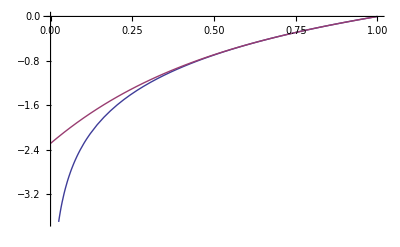

```mathematica
lnApprox[x_]=Normal[Series[Log[x+1],{x,0,5}]]/.x->(x-1)
Plot[{Log[x],lnApprox[x]},{x,0,1}]
```